Same principle as EulerLagrange1, I’m trying to work from scratch to get Kerr up and running and then we can see about cleaning it up and integrating it into the other versions. I think I’ve got it now and I know what in the other papers can be used as the initial conditions for the DiffGeo version. I’ll cover it as we go here.

```mathematica
(* Initial conditions *)
L0 = 1.74563;
E0 = 0.910514;
Q0=3.13238;
(*L0 = 3.72737;
E0 = 0.95845;*)
r0 = 10;
ϕ0 = 0;
t0=0;
θ0=Cos[π/4];
M0 = 1;
(*J0=0.5;*)
a0=0.998;
NullOrTimelike = -1;
```

```mathematica
(* Set the dimension and coordinate system *)
d = 4;
coords={t, r, θ, ϕ};
```

```mathematica
(* Define the metric (Kerr!) *)
rs =2M;
(*a=J/M;*)
Σ=r^2+a^2 Cos[θ]^2;
Δ=r^2-rs r + a^2;
ρ=r^2+a^2 Cos[θ]^2;
metric={{-1+(rs r)/Σ,0,0,(-rs r a)/Σ},{0,Σ/Δ,0,0},{0,0,Σ,0},{(-rs r a)/Σ,0,0,(r^2+a^2+(rs r a^2)/Σ Sin[θ]^2)Sin[θ]^2}};
metric//MatrixForm
inverseMetric=Simplify[Inverse[metric]];
```

(-1+(2 M r)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | -(2 a M r)/(r^2+a^2 Cos[θ]^2)
0 | (r^2+a^2 Cos[θ]^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | r^2+a^2 Cos[θ]^2 | 0
-(2 a M r)/(r^2+a^2 Cos[θ]^2) | 0 | 0 | Sin[θ]^2 (a^2+r^2+(2 a^2 M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)))

This is where we use the papers. Some of the papers have equations of motion derived from Euler-Lagrange (I think), this is where Niels got the integrals of motion with ρ that he transformed to Mino time. Set x^α to 0 and these equations can be used to find my initial velocities to solve the geodesic equations.
Going to use the eqs from Drasco and Hughes (2.1-2.4) but I think it’s equivalent to Schmidt and the rest.

```mathematica
ureq=((En(r^2+a^2)-a Lz)^2-Δ(r^2+(Lz-a En)^2+Q))/ρ^4;
uθeq=(Q-Cot[θ]^2 Lz^2-a^2 Cos[θ]^2(1-En^2))/ρ^4;
uϕeq=(Csc[θ]^2 Lz+a En((r^2+a^2)/Δ-1)-(a^2 Lz)/Δ)/ρ^2;
uteq=(En(((r^2+a^2)^2)/Δ-a^2 Sin[θ]^2)+a Lz(1-(r^2+a^2)/Δ))/ρ^2;

ur0=√(ureq) /.{r->r0, t->t0, ϕ->ϕ0, θ->θ0};
ut0=uteq/.{r->r0, t->t0, ϕ->ϕ0, θ->θ0};
uϕ0=uϕeq /.{r->r0, t->t0, ϕ->ϕ0, θ->θ0};
uθ0=√(uθeq) /.{r->r0, t->t0, ϕ->ϕ0, θ->θ0};

ur0/.{M->M0, a->a0, Q->Q0, En->E0}/.{Lz->L0};
ut0/.{M->M0, a->a0, Q->Q0, En->E0}/.{Lz->L0};
uϕ0/.{M->M0, a->a0, Q->Q0, En->E0}/.{Lz->L0};
uθ0/.{M->M0, a->a0, Q->Q0, En->E0}/.{Lz->L0};

ureq/.{r->r0, t->t0, ϕ->ϕ0, θ->θ0, M->M0, a->a0, Q->Q0, En->E0, Lz->L0}
uθeq//Simplify
uθeq/.{r->r0, t->t0, ϕ->ϕ0, θ->θ0, M->M0, a->a0, Q->Q0, En->E0, Lz->L0}
uϕeq//Simplify
uϕeq/.{r->r0, t->t0, ϕ->ϕ0, θ->θ0, M->M0, a->a0, Q->Q0, En->E0, Lz->L0}
```

-2.64941×10^-6

(Q+a^2 (-1+En^2) Cos[θ]^2-Lz^2 Cot[θ]^2)/((r^2+a^2 Cos[θ]^2)^4)

-1.11338×10^-8

(a (-a Lz+2 En M r)+Lz (a^2+r (-2 M+r)) Csc[θ]^2)/((a^2+r (-2 M+r)) (r^2+a^2 Cos[θ]^2)^2)

0.000428967

Now that we have initial positions and initial velocities, we should have enough to integrate the geodesic equations. We find them the same way as in the other notebooks, from the metric:

```mathematica
(* Calculate the Christoffel Symbol *)
Γ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ];
(* Ask Niels if this is a good way to go about it *)
(* Convert the general Christoffel connection to one where the coordinates are functions of time. Really I think this is swapping from the general connection to the connection between different paths or instances of the particle (i.e. we go from r as a coordinate to r_particle(τ) as a component of the position of this object) *)
ΓOfτ=Simplify[Table[(1/2)*Sum[(inverseMetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,d}],
{i,1,d},{j,1,d},{k,1,d}] ]/.{t->t[τ], r->r[τ], θ->θ[τ], ϕ->ϕ[τ]};
```

```mathematica
(* Get the geodesic equations for each component *)
u[α_]:=D[coords[[α]][τ],τ];
timeEq=t''[τ]+Sum[ΓOfτ[[1,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
radialEq=r''[τ]+Sum[ΓOfτ[[2,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
θEq=θ''[τ]+Sum[ΓOfτ[[3,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
ϕEq=ϕ''[τ]+Sum[ΓOfτ[[4,μ,ν]]u[μ]u[ν],{μ,1,4},{ν,1,4}];
```

```mathematica
EqsOfM={timeEq==0, radialEq==0, θEq==0, ϕEq==0,r[0]==r0, r'[0]==ur0, ϕ[0]==ϕ0, ϕ'[0]==uϕ0, t[0]==t0, t'[0]==ut0, θ[0]==θ0, θ'[0]==uθ0};
```

```mathematica
solRange=2000;
eomSol = Block[{M=M0, En=E0, Lz=L0, Q=Q0, a=a0}, NDSolve[EqsOfM, {r, ϕ, θ}, {τ, 0, solRange}]]
```

{{r→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],θ→InterpolatingFunction[…]}}

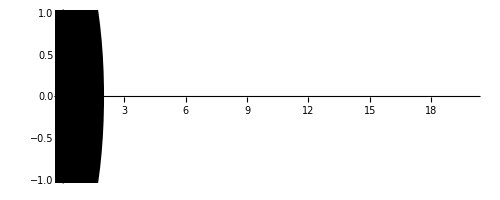

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```

```mathematica
ParametricPlot3D[{r[τ]Sin[θ[τ]]Cos[ϕ[τ]],r[τ]Sin[θ[τ]]Sin[ϕ[τ]], r[τ]Cos[θ[τ]]}/.eomSol, {τ, 0, solRange} ]
```

-Graphics3D-

```mathematica
Plot[r[τ]/.eomSol, {τ, 0, solRange}]
Plot[ϕ[τ]/.eomSol, {τ, 0, solRange}]
Plot[θ[τ]/.eomSol, {τ, 0, solRange}]
```

-Graphics-

-Graphics-

-Graphics-